```mathematica
SetDirectory["/home/remco/John Galt Holding/Universiteit Twente/Thesis/graphanalysis"]
```

/home/remco/John Galt Holding/Universiteit Twente/Thesis/graphanalysis

```mathematica
<<"candidates.mm"
```

```mathematica
Length[pkgs]
```

259

```mathematica
IdFor[str_]:=Position[pkgs,Select[pkgs,StringMatchQ[#,RegularExpression[".*"<>str<>".*"]]&]⟦1⟧]⟦1,1⟧
```

```mathematica
id=IdFor["lzma"]
data=deps[pkgs⟦id⟧];
max = Max[data];
curvepoints={2000+#/12,data⟦#⟧}&/@Range[Length[data]]//Select[#,(#⟦2⟧>0&)]&;
ListLinePlot[curvepoints, PlotRange->{0,max},Frame->None,Axes->False,ImageSize->{100,25},AspectRatio->Full]
Export["sparkline-"<>ToString[id]<>"-"<>StringReplace[pkgs⟦id⟧,"/"->"-"]<>".pdf",%]
```

173

-Graphics-

```mathematica
"
```

```mathematica
IdFor["lzma-utils"]
```

173

-Graphics-

```mathematica
Show[%685,ImageSize->{100,55},AspectRatio->Full]
```

-Graphics-

```mathematica
Show[%683,ImageSize->{55,55},AspectRatio->Full]
```

-Graphics-

```mathematica
Table[{i,pkgs[[i]]},{i,1,259}]//TableForm
```

1 | app-arch/bzip2
2 | app-arch/gzip
3 | app-arch/tar
4 | app-arch/sharutils
5 | media-sound/beep-media-player
6 | dev-util/cmake
7 | dev-libs/libgpg-error
8 | dev-libs/libedit
9 | dev-perl/extutils-pkgconfig
10 | media-libs/taglib
11 | media-libs/jasper
12 | dev-lang/yasm
13 | media-libs/libtheora
14 | dev-perl/Test-Pod
15 | dev-perl/DateTime
16 | x11-libs/cairo
17 | gnome-base/gnome-keyring
18 | net-dns/libidn
19 | x11-themes/hicolor-icon-theme
20 | dev-perl/DBD-SQLite
21 | dev-perl/Test-Exception
22 | dev-perl/Class-Accessor
23 | app-text/sword-modules
24 | dev-java/javahelp
25 | games-fps/ut2004
26 | dev-cpp/glibmm
27 | media-gfx/graphicsmagick
28 | app-emulation/emul-linux-x86-sdl
29 | games-server/ut2004-ded
30 | media-sound/gmpc
31 | app-emulation/emul-linux-x86-compat
32 | app-emulation/emul-linux-x86-soundlibs
33 | dev-java/ant-core
34 | dev-dotnet/gconf-sharp
35 | dev-dotnet/gnome-sharp
36 | dev-dotnet/glade-sharp
37 | sys-apps/hal
38 | gnome-extra/evolution-data-server
39 | dev-libs/liboil
40 | dev-java/ant-tasks
41 | dev-java/jruby
42 | dev-java/javatoolkit
43 | dev-perl/Test-Pod-Coverage
44 | dev-perl/File-Slurp
45 | app-shells/bash-completion-config
46 | app-crypt/qca
47 | sys-devel/autoconf-wrapper
48 | sys-devel/automake-wrapper
49 | rox-base/rox-lib
50 | dev-ruby/rubygems
51 | dev-ruby/rake
52 | media-sound/wavpack
53 | media-libs/libmodplug
54 | media-libs/freeglut
55 | media-fonts/dejavu
56 | dev-python/matplotlib
57 | sys-fs/fuse
58 | kde-base/libkdegames
59 | kde-base/konqueror
60 | kde-base/libkdepim
61 | kde-base/kode
62 | kde-base/libkcal
63 | kde-base/kwin
64 | dev-php/PEAR-PEAR
65 | dev-haskell/cabal
66 | dev-ruby/activesupport
67 | dev-python/pycairo
68 | app-text/gnome-doc-utils
69 | app-text/poppler
70 | dev-python/gst-python
71 | kde-base/kdebase-data
72 | sys-apps/sandbox
73 | dev-python/twisted-web
74 | app-text/asciidoc
75 | dev-db/libpq
76 | app-admin/eselect
77 | dev-python/lxml
78 | dev-python/gnome-python-extras
79 | media-libs/glew
80 | x11-apps/mkfontdir
81 | x11-apps/mkfontscale
82 | x11-misc/util-macros
83 | x11-libs/libX11
84 | x11-libs/libXp
85 | x11-libs/libXi
86 | x11-libs/libXaw
87 | x11-libs/libXmu
88 | x11-libs/libXt
89 | x11-libs/libICE
90 | x11-libs/libXext
91 | x11-libs/libxkbfile
92 | x11-libs/libXxf86dga
93 | x11-libs/libXrandr
94 | x11-apps/bdftopcf
95 | x11-libs/libXau
96 | media-fonts/encodings
97 | media-fonts/font-alias
98 | x11-libs/libXv
99 | x11-libs/libXxf86vm
100 | x11-libs/libXft
101 | x11-libs/libXScrnSaver
102 | x11-libs/libXrender
103 | x11-apps/xhost
104 | x11-libs/libXdmcp
105 | x11-libs/libXinerama
106 | x11-libs/libXtst
107 | x11-libs/libXcursor
108 | x11-libs/libXpm
109 | x11-libs/libSM
110 | x11-libs/libXfixes
111 | x11-libs/libdrm
112 | x11-libs/libXcomposite
113 | x11-libs/libXdamage
114 | x11-base/xorg-server
115 | net-dns/avahi
116 | media-tv/gentoo-vdr-scripts
117 | media-tv/vdrplugin-rebuild
118 | media-fonts/font-util
119 | media-fonts/font-cursor-misc
120 | media-fonts/font-misc-misc
121 | dev-libs/libnl
122 | games-fps/quake3-bin
123 | x11-misc/imake
124 | dev-python/setuptools
125 | app-admin/webapp-config
126 | x11-misc/gccmakedep
127 | media-libs/gst-plugins-base
128 | media-libs/gst-plugins-good
129 | app-text/hunspell
130 | x11-libs/libnotify
131 | sys-apps/man-db
132 | www-client/seamonkey
133 | dev-python/numpy
134 | dev-python/gnome-python-desktop
135 | media-gfx/exiv2
136 | dev-perl/List-MoreUtils
137 | sys-freebsd/freebsd-mk-defs
138 | media-libs/freealut
139 | dev-python/PyQt4
140 | net-libs/xulrunner
141 | app-text/ghostscript-gpl
142 | media-sound/pulseaudio
143 | x11-misc/xdg-utils
144 | dev-libs/dbus-glib
145 | dev-python/dbus-python
146 | dev-java/sun-jaf
147 | dev-python/pygobject
148 | x11-libs/libxcb
149 | net-misc/networkmanager
150 | dev-ruby/hoe
151 | dev-ruby/rspec
152 | mail-client/claws-mail
153 | dev-python/notify-python
154 | dev-java/ant-junit
155 | dev-java/ant-nodeps
156 | dev-java/ant-trax
157 | dev-python/simplejson
158 | dev-python/nose
159 | dev-haskell/mtl
160 | net-libs/telepathy-glib
161 | dev-python/pygments
162 | net-im/pidgin
163 | dev-cpp/eigen
164 | app-admin/eselect-vdr
165 | sec-policy/selinux-games
166 | dev-haskell/hscolour
167 | dev-ruby/mocha
168 | app-text/texlive-core
169 | dev-texlive/texlive-basic
170 | dev-texlive/texlive-documentation-base
171 | dev-texlive/texlive-latex
172 | dev-texlive/texlive-latexextra
173 | app-arch/lzma-utils
174 | dev-haskell/parsec
175 | x11-libs/qt-dbus
176 | x11-libs/qt-core
177 | x11-libs/qt-test
178 | x11-libs/qt-assistant
179 | x11-libs/qt-gui
180 | x11-libs/qt-opengl
181 | x11-libs/qt-qt3support
182 | x11-libs/qt-sql
183 | x11-libs/qt-svg
184 | x11-libs/qt-xmlpatterns
185 | x11-libs/qt-script
186 | x11-libs/qt-webkit
187 | x11-libs/qt-phonon
188 | app-admin/eselect-python
189 | kde-base/kdepimlibs
190 | kde-base/libkworkspace
191 | kde-base/kde-l10n
192 | dev-util/gtk-doc-am
193 | sys-apps/openrc
194 | dev-db/postgresql-base
195 | dev-db/postgresql-server
196 | x11-libs/qt-demo
197 | net-libs/webkit-gtk
198 | dev-util/xfce4-dev-tools
199 | x11-libs/libpciaccess
200 | dev-python/sphinx
201 | sys-libs/e2fsprogs-libs
202 | dev-python/libgnome-python
203 | dev-python/gnome-vfs-python
204 | dev-python/gconf-python
205 | dev-lang/vala
206 | media-libs/libcanberra
207 | app-office/akonadi-server
208 | media-libs/libv4l
209 | kde-base/plasma-workspace
210 | net-wireless/bluez
211 | dev-dotnet/glib-sharp
212 | dev-perl/Moose
213 | dev-dotnet/gtk-sharp-gapi
214 | dev-ruby/test-unit
215 | app-arch/xz-utils
216 | xfce-base/xfconf
217 | gpe-base/libgpewidget
218 | dev-libs/libunique
219 | xfce-base/exo
220 | kde-base/libknotificationitem
221 | kde-base/oxygen-icons
222 | dev-php/pear
223 | net-zope/zope-interface
224 | net-zope/zope-event
225 | net-zope/zope-schema
226 | net-zope/zope-i18nmessageid
227 | net-zope/zope-security
228 | net-zope/zope-component
229 | net-zope/zope-location
230 | x11-libs/qt-multimedia
231 | sys-auth/polkit
232 | xfce-base/libxfce4ui
233 | net-zope/zope-publisher
234 | net-zope/zope-traversing
235 | sys-infiniband/libibverbs
236 | x11-libs/qt-declarative
237 | dev-ruby/minitest
238 | dev-libs/gobject-introspection
239 | media-libs/clutter
240 | dev-vcs/git
241 | dev-vcs/bzr
242 | dev-vcs/mercurial
243 | sys-fs/udisks
244 | dev-lang/ruby-enterprise
245 | sys-power/upower
246 | dev-util/automoc
247 | media-libs/qimageblitz
248 | gnome-base/libgnome-keyring
249 | x11-libs/gdk-pixbuf
250 | dev-perl/Test-Fatal
251 | gnome-base/gsettings-desktop-schemas
252 | media-libs/phonon
253 | sys-apps/systemd
254 | dev-php/Horde_Exception
255 | dev-php/Horde_Translation
256 | dev-php/Horde_Util
257 | net-misc/leechcraft-core
258 | dev-php/ezc-Base
259 | x11-libs/qt-openvg

```mathematica
Pkg[id_]:={{id,pkgs⟦id⟧},ListLinePlot[deps[pkgs⟦id⟧],ImageSize->{600,350},PlotRange->{0,Max[deps[pkgs⟦id⟧]]}]}//Column
```

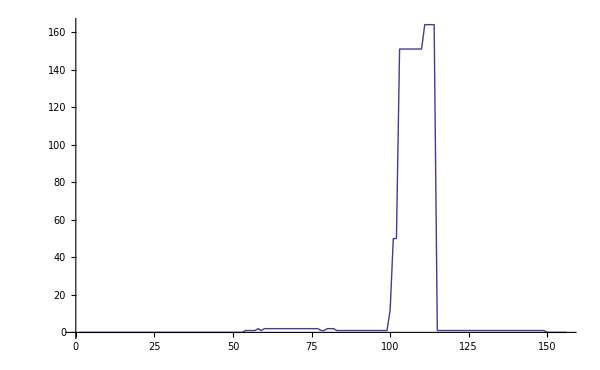
{23,app-text/sword-modules}
-Graphics-

```mathematica
Pkg[23]
```

```mathematica
Manipulate[Pkg[x],{x,1,Length[pkgs],1}]
```

```mathematica
IDs={34,65,218,157,240,242,17,206,193,143}
```

{34,65,218,157,240,242,17,206,193,143}

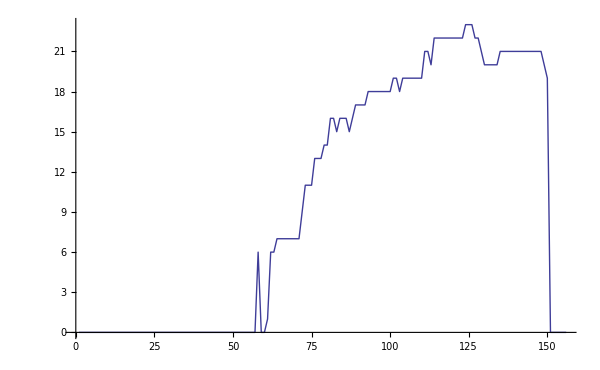
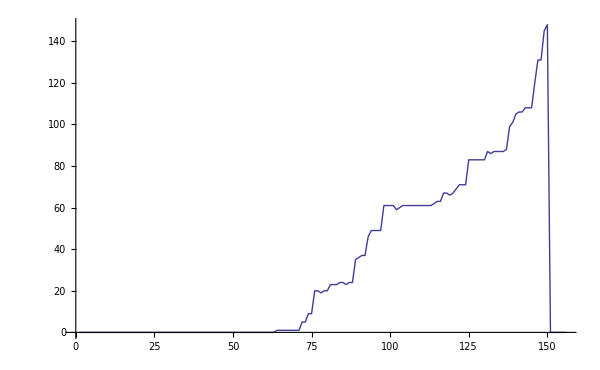
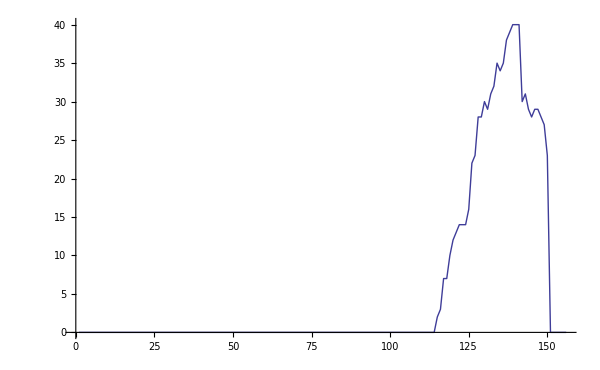
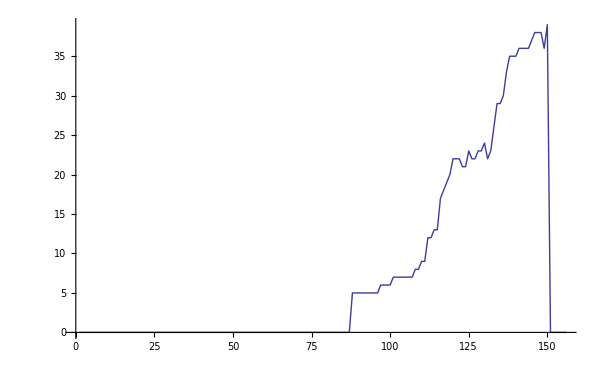
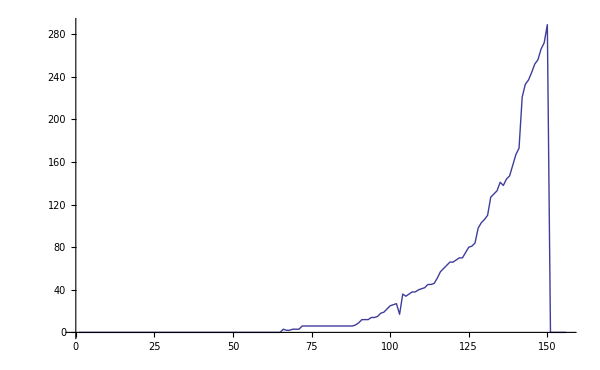
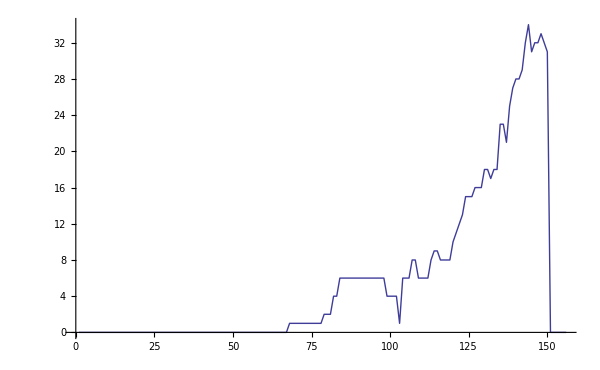
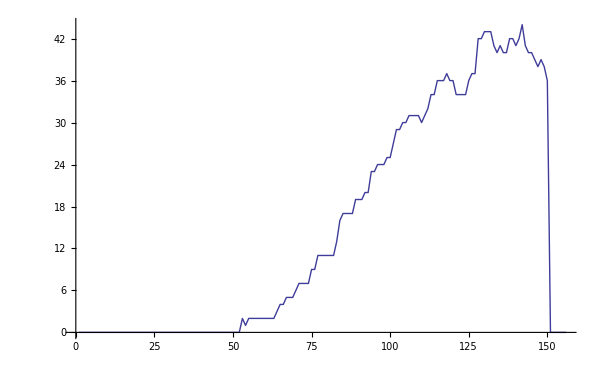
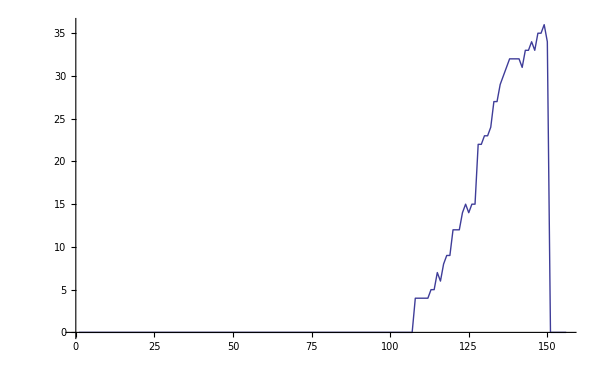
{34,dev-dotnet/gconf-sharp}
-Graphics-
{65,dev-haskell/cabal}
-Graphics-
{218,dev-libs/libunique}
-Graphics-
{157,dev-python/simplejson}
-Graphics-
{240,dev-vcs/git}
-Graphics-
{242,dev-vcs/mercurial}
-Graphics-
{17,gnome-base/gnome-keyring}
-Graphics-
{206,media-libs/libcanberra}
-Graphics-
{193,sys-apps/openrc}
-Graphics-
{143,x11-misc/xdg-utils}
-Graphics-

```mathematica
Table[Pkg[IDs[[x]]],{x,1,Length[IDs]}] //Column
```

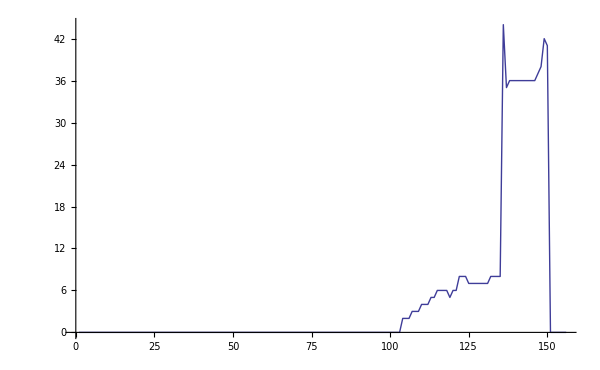
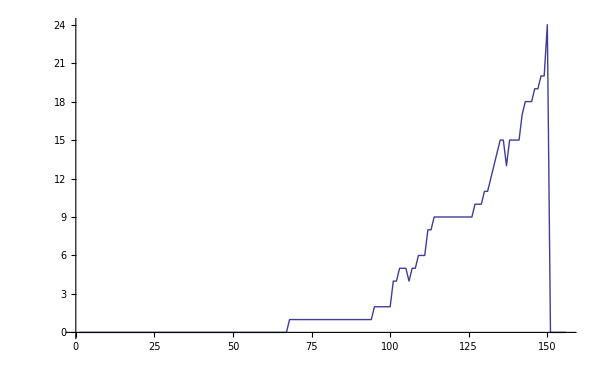
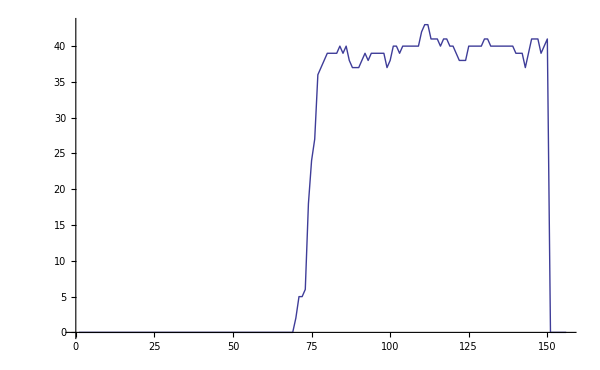
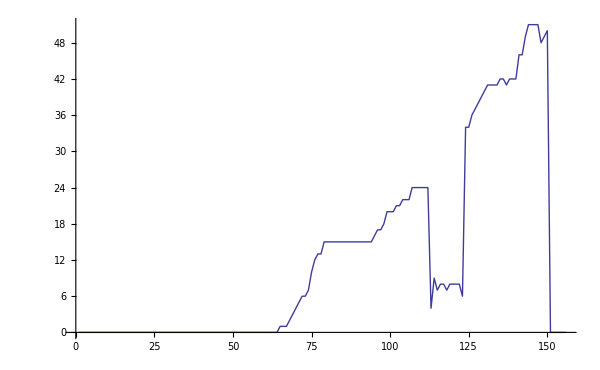
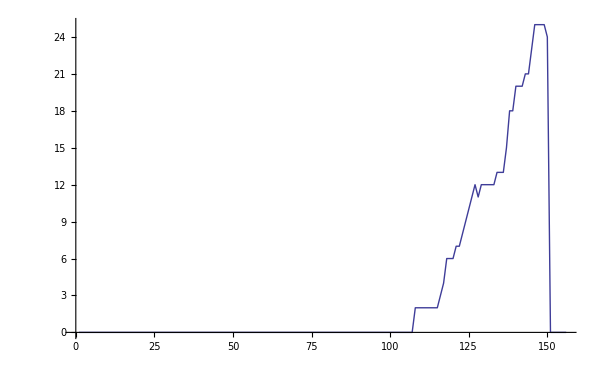
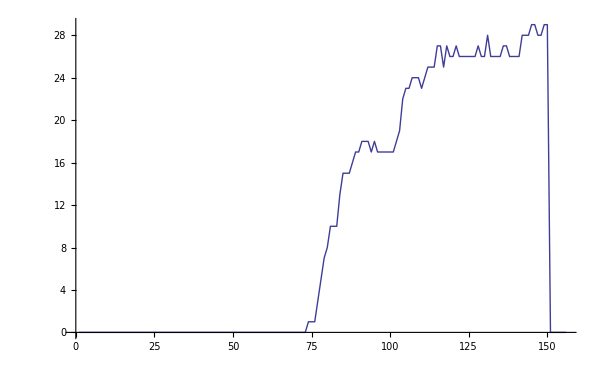
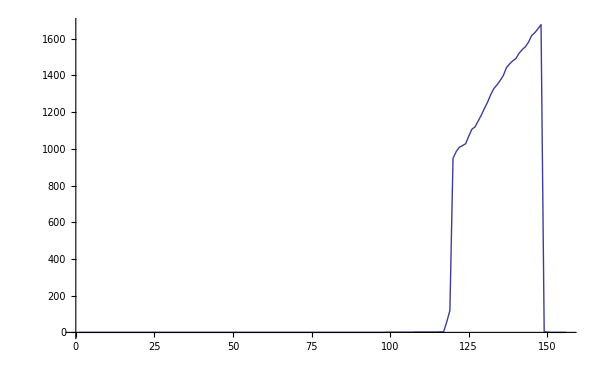
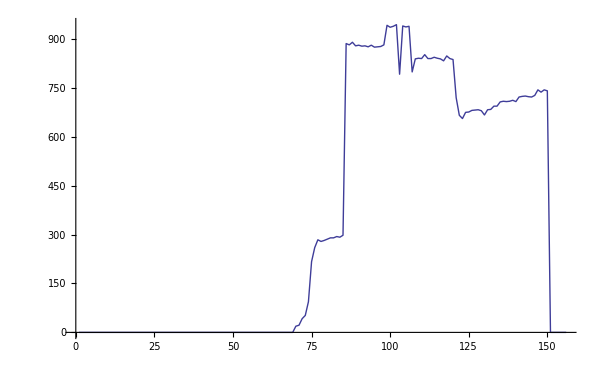
{{199,x11-libs/libpciaccess}
-Graphics-,{77,dev-python/lxml}
-Graphics-,{98,x11-libs/libXv}
-Graphics-,{218,dev-libs/libunique}
-Graphics-,{69,app-text/poppler}
-Graphics-,{208,media-libs/libv4l}
-Graphics-,{128,media-libs/gst-plugins-good}
-Graphics-,{188,app-admin/eselect-python}
-Graphics-,{88,x11-libs/libXt}
-Graphics-,{78,dev-python/gnome-python-extras}
-Graphics-}

```mathematica
Table[Pkg[RandomInteger[{0,259}]],{x,1,10}]
```